```mathematica
zeroonesign[x_, minus_]:= Sign[x-minus]
```

```mathematica
Checkerboard[mag_,latno_,lonno_,lat_,lon_, latoffset_, lonoffset_]:=mag*zeroonesign[Mod[lat-latoffset,360/latno], 360/latno/2]*zeroonesign[Mod[lon-lonoffset,360/lonno], 360/latno/2]
```

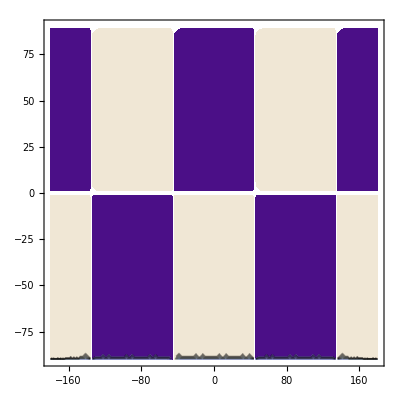

```mathematica
ContourPlot[Checkerboard[0.05,2,2,x,y,45,0],{x,-180,180},{y,-90,90}]
```

```mathematica
cmbspeed = 13.61
```

13.61

```mathematica
SlownessCheckerboard[mag_,latno_,lonno_,lat_,lon_, latoffset_, lonoffset_]:= (1/(Checkerboard[mag,latno,lonno,lat,lon, latoffset, lonoffset]+1) -1)/cmbspeed
```

```mathematica
synthvcheck = Flatten[Table[Table[{i,j,Checkerboard[0.05,2,2,j,i,0,0]},{j,-90,90}],{i,-180,180}],1];
```

```mathematica
Export[StringJoin[NotebookDirectory[],"synth_v_check.dat"],synthvcheck]
```

/Users/jackmuir/Dropbox/Honours/Code/scmb/synth_v_check.dat

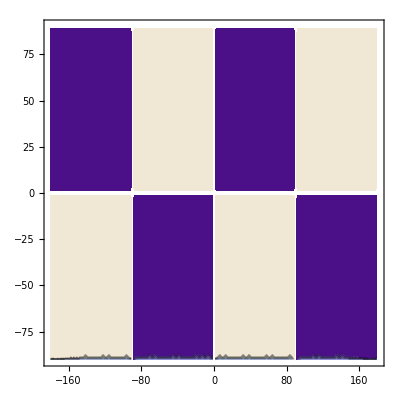

```mathematica
ContourPlot[SlownessCheckerboard[0.05,2,2,x,y,0,0],{x,-180,180},{y,-90,90}]
```

```mathematica
NotebookDirectory[]
```

/Users/jackmuir/Dropbox/Honours/Code/scmb/

```mathematica
pcpdata =Drop[Import[StringJoin[NotebookDirectory[],"ray_path_H_M_C_PcP_300km_Boschi.dat"]],1];
```

```mathematica
splitpcp = Select[SplitBy[pcpdata,Length[#]&], Length[#]=!= 1&];
```

```mathematica
toSynthTimes[mag_,latno_,lonno_, latoffset_, lonoffset_, listlist_]:= Total[Table[listlist[[i,4]]*SlownessCheckerboard[mag,latno,lonno,listlist[[i,2]],listlist[[i,3]], latoffset, lonoffset],{i,1,Length[listlist]}]]
```

```mathematica
vtimespcp = Table[toSynthTimes[0.05,2,2,0,0,splitpcp[[i]]],{i,1,Length[splitpcp]}];
```

```mathematica
p4kpdata =Drop[Import[StringJoin[NotebookDirectory[],"P4KP_PcP_Tanaka_Tomo.dat"]],1];
```

```mathematica
splitp4kp = Select[SplitBy[p4kpdata,Length[#]&], Length[#]=!= 1&];
```

```mathematica
vtimesp4kp = Table[toSynthTimes[0.05,2,2,0,0,splitp4kp[[i]]],{i,1,Length[splitp4kp]}];
```

```mathematica
rCore=3479.5;
vPlus=13.6601;
vMinus=8.0;
```

```mathematica
pcptopodata[[1]]
```

{{4.33817},{38.96,2891.5,363.,-63.48,78.15}}

```mathematica
-2 *(rCore^2/vPlus^2 -3.55^2)^0.5/rCore
```

-0.146398

```mathematica
pcptopodata=Partition[Drop[Import[StringJoin[NotebookDirectory[],"topo_in_H_M_C_PcP_Boschi.dat"]],1],2];
```

```mathematica
pcptorSynthTimes[mag_,latno_,lonno_, latoffset_, lonoffset_, listlist_]:= -2 * Checkerboard[mag,latno,lonno, listlist[[2]][[4]],listlist[[2]][[5]],latoffset, lonoffset] *(rCore^2/vPlus^2 - listlist[[1]][[1]]^2)^0.5/rCore
```

```mathematica
rtimespcp = Table[pcptorSynthTimes[5,2,2,45,45,pcptopodata[[i]]],{i,1,Length[pcptopodata]}];
```

```mathematica
synthrcheck = Flatten[Table[Table[{i,j,Checkerboard[5,2,2,j,i,45,45]},{j,-90,90}],{i,-180,180}],1];
```

```mathematica
Export[StringJoin[NotebookDirectory[],"synth_r_check.dat"],synthrcheck]
```

/Users/jackmuir/Dropbox/Honours/Code/scmb/synth_r_check.dat

```mathematica
timespcp = vtimespcp + rtimespcp;
```

```mathematica
Export[StringJoin[StringJoin[NotebookDirectory[],"synth_pcp.dat"]],Table[{1,timespcp[[i]]},{i,1,Length[timespcp]}]]
```

/Users/jackmuir/Dropbox/Honours/Code/scmb/synth_pcp.dat

```mathematica
p4kptopodata=Partition[Partition[SplitBy[Drop[Import[StringJoin[NotebookDirectory[],"P4KP_PcP_Tanaka_Topo.dat"]],1], Length[#]&],2],2];
```

```mathematica
Length[p4kptopodata[[1,1,2]]]
```

5

```mathematica
p4kptopodata[[1,1,2]]
```

{{122,359.205,3479.5,-7.956,122.271},{98,280.445,3479.5,-70.919,43.693},{74,201.685,3479.5,-13.298,-50.354},{50,122.925,3479.5,58.803,-89.37},{26,44.165,3479.5,34.297,138.498}}

```mathematica
p4kptorSynthTimes[mag_,latno_,lonno_, latoffset_, lonoffset_, listlist_]:= Module[{n =( Length[listlist[[1,2]]]-3)/2, pcpbounce= -2*(rCore^2/vPlus^2 - listlist[[2,1,1,1]]^2)^0.5/rCore, p4kpup = -(rCore^2/vPlus^2 - listlist[[1,1,1,1]]^2)^0.5/rCore,p4kpdown = (rCore^2/vMinus^2 - listlist[[1,1,1,1]]^2)^0.5/rCore},Checkerboard[mag,latno,lonno,listlist[[1,2,1,4]],listlist[[1,2,1,5]],latoffset,lonoffset]*p4kpup
+Checkerboard[mag,latno,lonno,listlist[[1,2,n,4]],listlist[[1,2,n,5]],latoffset,lonoffset]*p4kpdown
+Checkerboard[mag,latno,lonno,listlist[[1,2,n+1,4]],listlist[[1,2,n+1,5]],latoffset,lonoffset]*2*p4kpdown
+Checkerboard[mag,latno,lonno,listlist[[1,2,n+2,4]],listlist[[1,2,n+2,5]],latoffset,lonoffset]*2*p4kpdown
+Checkerboard[mag,latno,lonno,listlist[[1,2,n+3,4]],listlist[[1,2,n+3,5]],latoffset,lonoffset]*2*p4kpdown
+Checkerboard[mag,latno,lonno,listlist[[1,2,n+4,4]],listlist[[1,2,n+4,5]],latoffset,lonoffset]*p4kpdown
+ Checkerboard[mag,latno,lonno,listlist[[1,2,Length[listlist[[1,2]]],4]],listlist[[1,2,Length[listlist[[1,2]]],5]],latoffset,lonoffset]*p4kpup
- Checkerboard[mag,latno,lonno,listlist[[2,2,1,4]],listlist[[2,2,1,5]],latoffset,lonoffset]*pcpbounce]
```

```mathematica
rtimesp4kp = Table[p4kptorSynthTimes[5,2,2,45,45,p4kptopodata[[i]]],{i,1,Length[p4kptopodata]}];
```

```mathematica
timesp4kp = vtimesp4kp + rtimesp4kp;
```

```mathematica
Export[StringJoin[StringJoin[NotebookDirectory[],"synth_p4kp.dat"]],Table[{1,timesp4kp[[i]]},{i,1,Length[timesp4kp]}]]
```

/Users/jackmuir/Dropbox/Honours/Code/scmb/synth_p4kp.dat

```mathematica
Y[l_,m_,θ_,ϕ_]:= Abs[Piecewise[{{SphericalHarmonicY[l,m,θ,ϕ],m==0},{(1/√2)*(SphericalHarmonicY[l,-m,θ,ϕ]+(-1)^m SphericalHarmonicY[l,m,θ,ϕ]),m>0},{(I/√2)*(SphericalHarmonicY[l,-m,θ,ϕ]-(-1)^m SphericalHarmonicY[l,m,θ,ϕ]),m<0}}]]
```

```mathematica
ModelV[lat_,lon_]:= Module[{θ=-(lat-90)*π/180.0,ϕ=lon*π/180.0},-0.02Y[2,-2,θ,ϕ] + 0.04Y[4,1,θ,ϕ]+0.01Y[4,-4,θ,ϕ]]
ModelVt[lat_,lon_]:= (1/(ModelV[lat,lon]+1) -1)/cmbspeed
ModelR[lat_,lon_]:= Module[{θ=-(lat-90)*π/180.0,ϕ=lon*π/180.0},-1.0Y[4,2,θ,ϕ] + 5.0Y[3,3,θ,ϕ]-1.5Y[1,-1,θ,ϕ]]
```

```mathematica
p4kptoRYmag[listlist_]:= Module[{n =( Length[listlist[[1,2]]]-3)/2, pcpbounce= -2*(rCore^2/vPlus^2 - listlist[[2,1,1,1]]^2)^0.5/rCore, p4kpup = -(rCore^2/vPlus^2 - listlist[[1,1,1,1]]^2)^0.5/rCore,p4kpdown = (rCore^2/vMinus^2 - listlist[[1,1,1,1]]^2)^0.5/rCore},ModelR[listlist[[1,2,1,4]],listlist[[1,2,1,5]]]*p4kpup
+ModelR[listlist[[1,2,n,4]],listlist[[1,2,n,5]]]*p4kpdown
+ModelR[listlist[[1,2,n+1,4]],listlist[[1,2,n+1,5]]]*2*p4kpdown
+ModelR[listlist[[1,2,n+2,4]],listlist[[1,2,n+2,5]]]*2*p4kpdown
+ModelR[listlist[[1,2,n+3,4]],listlist[[1,2,n+3,5]]]*2*p4kpdown
+ModelR[listlist[[1,2,n+4,4]],listlist[[1,2,n+4,5]]]*p4kpdown
+ModelR[listlist[[1,2,Length[listlist[[1,2]]],4]],listlist[[1,2,Length[listlist[[1,2]]],5]]]*p4kpup
- ModelR[listlist[[2,2,1,4]],listlist[[2,2,1,5]]]*pcpbounce]
```

```mathematica
pcptoRYmag[ listlist_]:= -2 * ModelR[ listlist[[2]][[4]],listlist[[2]][[5]]] *(rCore^2/vPlus^2 - listlist[[1]][[1]]^2)^0.5/rCore
```

```mathematica
toVYmag[listlist_]:= Total[Table[listlist[[i,4]]*ModelVt[listlist[[i,2]],listlist[[i,3]]],{i,1,Length[listlist]}]]
```

```mathematica
synthvylm= Flatten[Table[Table[{i,j,ModelV[j,i]},{j,-90,90}],{i,-180,180}],1];
```

```mathematica
Export[StringJoin[NotebookDirectory[],"synth_v_ylm.dat"],synthvylm]
```

/Users/jackmuir/Dropbox/Honours/Code/scmb/synth_v_ylm.dat

```mathematica
synthrylm= Flatten[Table[Table[{i,j,ModelR[j,i]},{j,-90,90}],{i,-180,180}],1];
```

```mathematica
Max[synthrylm[[;;,3]]]
```

2.47713

```mathematica
Export[StringJoin[NotebookDirectory[],"synth_r_ylm.dat"],synthrylm]
```

/Users/jackmuir/Dropbox/Honours/Code/scmb/synth_r_ylm.dat

```mathematica
vtimespcp = Table[toVYmag[splitpcp[[i]]],{i,1,Length[splitpcp]}];
```

```mathematica
rtimespcp = Table[pcptoRYmag[pcptopodata[[i]]],{i,1,Length[pcptopodata]}];
```

```mathematica
timespcp = vtimespcp + rtimespcp;
```

```mathematica
vtimesp4kp = Table[toVYmag[splitp4kp[[i]]],{i,1,Length[splitp4kp]}];
```

```mathematica
rtimesp4kp = Table[p4kptoRYmag[p4kptopodata[[i]]],{i,1,Length[p4kptopodata]}];
```

```mathematica
timesp4kp = vtimesp4kp + rtimesp4kp;
```

```mathematica
SeedRandom["!!!SHADATASETUP!!!"]
randtimespcp = Table[timespcp[[i]]+0.15*RandomReal[NormalDistribution[0,1]],{i,1,Length[timespcp]}];
randtimesp4kp = Table[timesp4kp[[i]]+0.1*RandomReal[NormalDistribution[0,1]],{i,1,Length[timesp4kp]}];
```

```mathematica
Export[StringJoin[StringJoin[NotebookDirectory[],"synth_pcp_ylm.dat"]],Table[{1,randtimespcp[[i]]},{i,1,Length[timespcp]}]]
```

/Users/jackmuir/Dropbox/Honours/Code/scmb/synth_pcp_ylm.dat

```mathematica
Export[StringJoin[StringJoin[NotebookDirectory[],"synth_p4kp_ylm.dat"]],Table[{1,randtimesp4kp[[i]]},{i,1,Length[timesp4kp]}]]
```

/Users/jackmuir/Dropbox/Honours/Code/scmb/synth_p4kp_ylm.dat

```mathematica
randtimesp4kp
```

{0.619979,0.746023,0.720704,0.737362,0.596084,0.66017,0.650863,0.613844,0.942389,0.859463,0.949108,1.03315,0.608233,0.39782,0.965554,0.8555,0.89522,0.983293,0.355466,1.03335,0.902297,0.965555,0.951396,0.679532,0.925635,0.978924,0.673591,0.705555,0.845173,0.766674,1.36053,0.400272,0.360048,0.532402,1.06532,0.131804,-0.446656,-0.457345,-1.57531,1.707,0.902774,-0.145238,-0.332971,-0.0457627,-0.214393,-0.0252942,0.788208,-0.342743,-0.210357,-0.324355,-0.29784,-0.0513065,-0.230028,-0.227364,-0.186845,-0.310306,-0.321442,-0.331505,-0.054207,-0.0733739,0.780884,-0.0791246,-0.0817388,0.71416,0.0503707,0.0373779,0.00808028,-0.104469,0.83732,0.115858,-0.0617559,0.379737,0.56847,-0.0929764,0.143858,0.0861061,0.567706,-2.4357,-1.63047,0.172137,-1.71091,0.837847,-1.8735,-1.85171,-1.8411,-2.03082,0.623892,-2.03533,-1.85522,-1.88226,-1.87918,0.912076,-0.356009,-0.293952,-0.289708,-0.188587,-0.299244,-0.204378,-0.361168,-0.250655,-0.380947,-0.418086,-0.405243,-3.49944,0.774918,0.441129,-0.948743,0.76366,0.583319,0.51565,0.919991,0.904844,0.205549,-1.48552,0.17904,0.0885535,-0.46374,-0.624674,0.164723,0.112669,0.0460627,-0.44828,-0.586177,-0.0608685,-0.583736,-0.58706,-0.642742,-0.582888,0.0709291,-0.562667,-0.147222,-0.624845,0.168159,-0.584393,-0.237843,-0.581623,-0.352768,-0.601847,0.181074,0.0747119,-0.598121,0.120246,-0.160857,-0.601636,-0.563421,0.157157,0.0690626,0.163161,-0.539297,-0.46644,-0.444954,-0.628417,-0.0307314,-0.615668,0.0411176,0.0634267,0.0390643,-0.608825,0.148264,-0.0248247,-0.619197,-0.5824,-0.608028,-0.597942,-0.632294,-0.435339,0.0429833,-0.277189,-0.0155148,-0.591415,-1.41809,0.441957,-1.92181,-2.28093,-0.0541002,-1.38669,-1.31895,-1.33369,-2.72903,-2.11765,-1.98602,-1.82209,-1.98184,-0.615853,-2.0873,-2.28329,-1.5282,-0.436809,-0.238534,-4.32208,0.407961,-3.75674,-2.0657,0.297577,-0.256653,-2.69639,-0.237558,-2.73416,-2.74401,-3.05642,-2.55534,-2.74235,-2.82272,-2.70391,-2.51538,-2.39447,-2.68948,-2.87595,-2.91693,-2.6153,-1.30986,-1.4186,-1.60056,-1.55361,-1.31588,-0.0324474,-1.94831,-2.22799,-2.07173,-1.37065,-1.3285,-2.92734,-1.40318,-1.47365,0.106197,0.183358,0.10499,-0.516053,0.188329,0.129078,0.0599618,-0.0507003,0.2099,-0.0273088,0.191708,-0.383337,0.1373,0.174412,-0.464005,-0.434446,0.072173,0.0594051,0.0994528,0.179534,0.158998,-0.389895,-0.386437,-0.42407,0.0636295,-0.000714547,-1.54502,-3.33415,-0.332117,-0.354094,-0.309397,0.417829,0.378207,-0.421056,0.378086,0.350051,-0.476319,-0.439341,-0.756747,-0.472988,-0.351045,0.840189,-0.367099,0.408455,0.313334,0.0132869,0.306546,0.360519,0.416385,-0.36677,-0.428323,1.23189,0.423996,0.286441,0.2681,0.284884,-0.324057,-0.371668,0.786436,-0.0158943,0.373061,0.181147,-0.237547,0.406433,-0.572417,0.26176,0.267143,0.280755,0.436456,0.404431,-0.254576,0.23187,0.384808,0.275528,0.418465,0.517744,0.62316,-0.327191,0.454779,0.423204,0.361328,0.365037,-0.382759,0.264696,-0.393988,-0.485493,-0.139331,-0.681495,0.366613,-0.458013,0.11421,0.117848,-0.533967,-0.53725,-0.550482,0.0943744,0.0978365,-0.243232,0.00507503,0.120611,0.469005,0.078058,-0.514659,-0.485823,-0.755474,-1.13676,-2.7442,-0.673989,-1.39833,-1.03909,-3.17052,-0.109039,-0.20829,-0.0326115,-0.0769605,-0.182467,1.08154,1.09425,1.21996,0.730846,0.883029,0.978007,-1.29795,-0.0631699,0.888107,-1.68722,-1.30164,0.834619,0.523539,0.757637,0.287522,0.672217,0.681926,-0.455272,0.876405,0.950843,0.751901,-1.06061}

```mathematica
randtimespcp
```

{-0.755345,-1.66107,-1.03462,-1.22389,-0.474256,-0.648255,-0.652278,-1.16932,-0.878559,-0.834642,-0.457303,-0.633182,-0.658649,-1.41818,-0.481063,-2.26269,-0.505993,-0.793785,-0.130151,-0.55168,0.0225164,0.0620051,-0.383721,-0.528318,-0.881279,-1.4659,-1.5335,-1.45148,-1.51069,-1.51942,-1.58821,-1.33288,-1.33945,-1.24134,-1.68765,-1.42801,-1.41107,-1.51911,-2.02294,-0.227958,0.0125903,0.0421537,-0.278173,0.0645953,-0.131897,-0.0338841,-0.269203,-0.982851,-1.76255,-1.70507,-1.28947,-1.95734,-1.1546,-0.097989,-1.82855,0.0804868,-1.55806,-0.650914,-0.971564,0.0564711,-0.0136471,-0.28669,-0.0477255,0.0642486,0.0638341,0.0559533,0.0455006,0.0555721,0.0252922,0.035993,-0.0610604,-1.25121,-0.649319,-0.531016,-0.521928,-0.239599,-0.591497,-0.536617,-0.606936,-0.577169,-0.527392,-0.630773,-0.603254,0.0215184,-0.0547796,-0.914407,-0.697325,-0.9074,-0.125536,-0.705758,-0.240622,-1.27681,-0.572048,-0.577789,-1.13833,-0.55084,-1.32391,-1.18654,-1.30619,-1.18511,-1.31871,-0.736698,-1.38258,-1.16188,0.0191723,-0.311835,-0.465139,-0.705273,-0.330974,-0.00504939,-1.75267,-2.40232,-2.46273,-2.21785,-2.26312,-1.22608,-1.09911,-0.966036,-0.87625,-1.33028,-1.07179,-0.990737,-1.05346,-1.03972,-1.00522,-1.06148,-1.12239,-1.12589,-1.10556,-0.908334,-1.12428,-0.86007,-1.02564,-1.48302,-1.17993,-1.06163,-0.178656,-0.569449,-0.172279,-0.836298,-0.0125518,-1.2583,-0.669348,-1.98986,0.0918248,0.0904099,0.0965256,-0.0879736,-0.076653,-0.0499261,0.0570504,0.0648783,-1.05937,-0.148135,0.0390075,-0.105677,-0.100864,-0.0544414,-0.125134,-0.238492,-0.554022,-0.547085,-0.375922,-0.379301,-0.257141,-0.408737,-0.116012,-1.85018,-0.551033,-1.10318,-0.545711,-0.452319,-0.155137,-0.601934,-0.285182,-0.227382,0.101287,-0.575529,-0.942677,0.0876118,0.10282,-0.159983,-0.0122682,0.0598849,0.0343435,-0.405287,0.0953851,-0.579129,-0.702306,0.0582542,0.062365,0.0541268,-0.625838,-0.476277,0.08384,-0.0938228,-1.42112,-1.48474,-1.22702,-2.12755,-0.0696682,-0.4786,-0.150278,-1.22914,-0.645929,-0.106884,-1.882,-1.3247,-1.24271,-1.23697,-0.8617,0.100131,-1.14127,-1.00491,-2.1169,-1.05569,-0.517265,-0.437284,-0.544868,-0.698725,-0.637023,-0.514715,-0.571896,-2.0478,-1.40898,-1.33404,-1.41733,-1.47526,-1.47571,-1.54684,-1.35828,-2.07931,-1.76207,-1.99277,-1.84799,-1.79773,-1.4689,-0.333495,-0.543359,0.0565722,-0.477999,0.0877693,0.0890801,0.0495349,0.055115,0.0364772,0.0561237,0.0729258,0.0484332,0.0147428,0.046885,0.0490767,0.0389671,-0.138428,0.0024965,-0.538589,0.00607422,0.111559,0.0406377,-1.72526,-0.200868,0.00879882,-0.0144983,0.0689673,-0.464653,-0.268461,-0.592104,-1.76565,-1.62029,-2.19331,-0.0355753,-0.308314,-0.751742,-0.456099,-1.01333,-0.149275,-0.137741,0.0749909,-2.05936,0.0637127,-0.582236,-0.0266148,-0.304828,-0.0142306,-0.101164,-0.472511,-0.948136,-1.52292,0.0834275,-0.754729,-0.232822,-0.587395,-2.02871,-0.0862781,-1.03945,-1.84127,-0.39135,-0.234644,0.166176,-0.645332,-0.0435845,-0.20066,-0.00437117,0.00669506,-0.184466,-0.143299,-0.276762,-2.00809,-1.01983,-1.04484,-0.904912,-0.240166,-0.353732,-0.267328,-0.635831,-0.597685,-0.612105,-1.02666,-0.225759,-0.322543,-0.0978717,-0.833648,-1.01734,-1.36208,-1.62912,-1.6463,-0.243586,-0.190585,-0.401123,0.0676112,-0.539658,-0.196073,-1.21448,-2.0011,-1.27008,-1.39607,0.0103887,-1.30767,0.137798,-0.237795,-0.267886,-0.105113,-0.243688,-0.226944,-0.280619,-0.208989,-0.233394,-0.185404,-0.188621,-0.144554,-1.37853,0.0355696,0.0779362,-0.0469232,-0.263071,-0.19179,-0.19802,-0.193058,-0.19679,-0.177801,-0.185928,-0.0864845,0.0180178,-0.0511414,-0.436339,-0.242448,0.0535319,-0.682368,-0.0123746,-0.0466425,0.0236492,0.037662,0.068332,-1.78645,0.0548057,-0.0959423,-0.0572733,-0.710568,0.00173032,-0.337824,-0.112455,-0.141558,-0.175352,-0.5178,-0.0537986,-0.0770541,-0.781887,-0.786053,-0.171307,0.237017,-1.61894,-0.668952,-0.697143,-0.262575,-0.366201,-0.746931,-1.38835,-2.03032,-0.211536,0.110617,0.0519552,-0.0587716,-0.534898,-0.758625,-0.0756715,-0.37288,-0.726277,-1.24288,-1.17764,-1.52739,0.112228,-1.47999,-2.05741,-1.66732,-1.7238,-2.20802,-0.975285,-1.51872,-0.768207,-0.625983,-2.04021,-1.82933,-2.07224,-2.10581,-1.2249,-0.526681,-0.877057,-1.8896,-2.03244,-1.10043,-1.10371,-1.12437,0.273348,-0.364357,-1.59904,-0.274415,-0.726122,-1.59194,-0.931457,-0.719782,-0.2895,-0.72983,-0.424765,-0.810954,-0.204439,-0.461055,-1.57363,-0.479957,-0.153514,-0.0871876,-0.0633782,0.0101346,-1.28035,0.251819,-1.16283,-0.765437,-0.433309,-0.731516,-0.851219,-0.0337866,0.177877,-0.145265,-0.789804,-0.807384,-0.206253,-0.52998,-0.661672,-0.0282011,-0.147278,-0.474681,-1.34012,0.300113,-0.366937,-0.0560241,-1.77453,-1.73454,-0.601347,-0.384746,-1.01,-1.03386,-1.86822,0.152731,0.16738,-1.00942,-1.15462,-0.279286,-1.52306,-1.52312,-1.11384,-1.29471,-0.704007,-0.779116,-0.446158,-0.726769,-1.62329,-0.384123,-0.152924,-0.390428,-0.161247,-1.65738,-0.415028,-0.900003,-0.888875,-1.76446,-0.904943,-0.392275,-0.308293,-2.00524,-2.11201,-0.201678,-0.368804,-0.490722,-0.71568,-0.686355,-0.432994,-0.115391,0.00016367,0.0072523,-0.462723,-0.00528864,-0.0621528,-0.0839293,-0.0232308,-0.167506,-1.17809,-0.573449,-0.258526,-0.207891,-0.396174,-0.390698,-0.380738,-0.182157,-1.42695,-1.93248,-1.94362,-1.03413,-1.86083,-1.82543,-1.8412,-0.43392,-0.615446,-0.874914,0.0184104,-0.150873,-0.16081,-0.158342,-0.115314,-0.702085,-0.704552,-1.12081,-0.216339,-0.154764,-0.424157,-0.0451738,-0.233484,0.0383499,-0.107257,-0.0585314,-2.17161,-0.145436,-0.0520603,-0.106439,-1.68993,-0.110287,-0.445609,-0.436,-0.462553,-0.49182,-0.509678,-0.458499,-0.664025,-0.72161,-0.620343,-0.663671,0.0977629,0.245625,-0.727074,-0.571352,-0.569987,-0.607539,-0.582148,-0.77238,-1.11107,-0.564363,-1.13754,0.0553558,-0.691309,-0.748142,-0.947879,-1.56356,-0.515094,-0.477685,-1.02295,-1.08819,-0.220027,-1.13317,-0.0181974,-0.397471,-0.381477,-0.452018,-0.0566949,-0.368022,-0.446257,-0.0555819,-0.394791,-1.76515,-0.463791,-1.91183,-0.997372,-1.63889,-2.06852,-1.89299,-0.96629,-1.01722,-0.572115,-1.30672,-1.01194,-1.48208,-1.19276,-0.985718,-1.68124,0.207135,-1.06563,-0.237595,-0.540319,-0.66553,-0.658285,-0.31473,-0.411253,-0.120461,0.174231,-0.0736508,-0.369105,-1.16429,-1.43534,-1.5862,-1.2708,-1.49162,-0.34965,-0.17032,-2.25972,-1.0861,-1.99239,-0.467027,-1.26769,-1.16418,-0.363931,-1.37572,-1.23393,-0.916461,-1.38112,-0.823405,-1.75024,-0.932252,-0.922237,-1.7523,-1.41816,-0.418844,-1.65426,-0.211306,-0.0547238,-0.844051,-1.6465,-0.837335,-0.445482,-0.0590345,-1.07555,-0.524215,-0.00872163,-0.442493,-1.23128,-0.727725,-0.00656566,-0.761319,-1.49092,-2.04434,-1.45746,-2.05317,-1.86749,-1.55123}

```mathematica
timespcp - randtimespcp
```

{0.0144806,-0.0255567,0.013687,0.059274,0.0225844,-0.00913229,-0.0338603,-0.0310944,-0.0178837,0.0920051,0.0104686,-0.0183529,-0.0458243,0.00639595,-0.0234043,0.159981,-0.0175599,0.0499014,0.00489063,-0.0470625,-0.00158707,-0.000683553,-0.0535108,-0.0299859,0.0119236,0.0710937,-0.0281607,0.135556,0.0731005,-0.0905158,-0.0173545,-0.0857161,-0.00748142,-0.0932382,0.0358322,-0.0391293,0.000638851,0.211603,-0.0178545,0.00332323,0.000209711,-0.00119409,0.00753256,-0.000416582,0.0155414,0.00215201,-0.00323977,-0.0164438,0.0495266,0.127209,0.112931,-0.131249,-0.0778771,-0.00542509,0.0261898,-0.000846125,0.0875971,0.0253458,0.0667992,0.000259529,-0.00103434,-0.00310156,-0.000309744,0.0000788702,-0.00172808,0.000205187,0.00278098,-0.00258695,0.00183713,-0.00203812,-0.00114099,0.0236339,-0.0820002,-0.0633728,-0.026039,-0.0125436,0.008325,-0.0460779,0.0119901,-0.0130671,-0.0564808,0.0396869,0.0115928,0.00168488,0.00116713,0.0548609,0.00255971,0.0139806,-0.00218222,0.0142616,0.000775141,0.0138084,0.0289019,0.00334116,0.0324243,0.0241714,0.00128637,-0.0189054,0.0743763,-0.0630153,0.013551,-0.0779176,0.00217154,-0.0535026,0.0025546,-0.00385991,0.000779029,-0.0598701,0.02316,0.000026288,-0.10758,-0.133547,0.0992121,0.0714302,-0.114701,0.0199898,0.147193,-0.0421085,-0.00608885,0.0787193,-0.0378544,-0.0713444,-0.00560782,-0.0169998,-0.0543922,0.00300899,0.0472791,0.0495149,0.0334919,-0.0465031,-0.0573364,-0.0043112,0.00918819,0.0219983,0.0205884,-0.0665399,0.00165305,0.0187253,-0.00645782,-0.0642278,-0.000407318,0.0369728,-0.0344713,-0.11795,-0.0025621,-0.000175745,-0.00685069,-0.00155678,-0.00106193,-0.000754816,0.00130465,0.00203952,0.0246086,0.00209778,-0.00149015,0.00957174,0.00559214,0.00130811,-0.00179247,0.00485329,0.00752791,0.00218928,-0.024046,0.0143359,0.00742853,-0.000377768,0.0060347,0.050811,-0.0422349,-0.0365925,0.0139533,-0.043241,-0.00346326,0.0114355,-0.0114763,0.0121315,-0.00436167,-0.0373435,0.0480542,0.00213375,-0.00652646,-0.00895472,0.000978737,-0.000647671,0.0029835,-0.0150573,0.0114914,-0.0710117,-0.00504868,0.0013376,-0.00423179,-0.00396693,-0.0738892,-0.0120179,0.00263206,0.000211941,-0.0332388,0.0435239,0.0405688,-0.281444,-0.000413521,-0.0111319,-0.019263,0.0740951,-0.0438668,-0.00207576,-0.140901,0.0154145,-0.0430367,0.080734,-0.012477,-0.0015029,-0.0312998,-0.0743296,0.0141849,-0.025245,0.0367064,-0.024334,-0.0107338,0.0149725,-0.0292802,-0.0314891,0.0556597,0.0193791,-0.00053388,-0.0791877,0.00854618,0.012533,0.0714214,0.0595116,-0.0188146,0.0535064,-0.0212927,-0.135886,-0.00568786,0.0488643,-0.0247179,-0.00643864,-0.029535,-0.000952572,0.0258797,-0.00187188,0.000992346,0.00132481,-0.00197022,0.00353741,0.0045995,0.00391277,0.00106959,0.000731144,-0.000891602,0.00218508,-0.00247095,0.0142022,-0.0000723129,-0.0261704,-0.000244358,-0.0104362,-0.0010185,-0.0256222,-0.00453114,0.000126367,-0.00125039,-0.00156212,-0.00741446,0.00935248,-0.0162962,-0.0105002,-0.155198,0.0881414,0.00208294,0.00729065,-0.000495524,0.0177983,0.0261315,0.00373417,0.00520075,0.00304604,-0.0912107,-0.00476762,0.051295,-0.0000458603,0.00421931,-0.000657461,-0.0084496,-0.0102184,0.0165476,-0.0715412,-0.00588564,0.00338075,-0.0000550605,0.00982379,-0.0763787,-0.0080382,-0.0534571,-0.147727,0.00482203,0.00881738,-0.0135745,0.00888353,0.00125739,0.0000427478,0.0000950086,-0.000671351,0.0143185,0.00472877,0.0159339,-0.0325902,0.0301743,0.0696344,0.0522267,-0.0142978,0.00316445,-0.00280471,0.04784,-0.0158353,-0.0104002,0.0422997,-0.012558,0.00261052,0.00497975,-0.0300894,-0.0614753,0.0240038,0.0591958,-0.0478565,-0.00500133,-0.00297421,-0.0115074,0.00591955,0.0125099,0.0185703,0.0635974,0.130496,-0.0989109,0.123185,0.000295884,0.0255184,0.0111494,0.00306518,0.00374884,-0.00529922,0.00772119,-0.0150613,0.00628104,0.00491605,0.0154546,-0.0162646,-0.0135444,0.00553307,-0.000949888,0.0000694031,-0.00589159,0.000131174,0.0042147,-0.00330382,0.00474485,-0.00252251,-0.000604067,-0.00978115,-0.000799916,-0.00604009,0.00199284,-0.00296756,-0.00614676,0.0011719,-0.00116587,0.00561806,0.000254694,-0.000167889,0.000104846,-0.00015313,-0.00280031,0.0471935,-0.00469866,0.00277428,-0.0022015,0.00168883,0.00011184,0.0141989,-0.00180127,0.00851033,0.0128925,-0.0289398,0.00142707,-0.00480286,-0.0410788,-0.0545653,-0.00839526,-0.0035832,0.0200174,-0.0819295,0.00847338,0.011958,0.0206013,-0.00604732,-0.00901347,0.13659,0.0120422,0.000374392,-0.00262605,0.00151344,0.00801402,0.022009,-0.00348191,-0.0284477,0.0121704,0.00433047,-0.0494228,-0.162346,-0.00450376,-0.128148,0.113432,-0.137565,-0.0562999,0.159865,0.0374672,0.00477657,0.0681323,-0.0096758,0.0726661,-0.166672,0.0148529,0.0494804,-0.0621269,-0.0241485,-0.000614851,0.179546,-0.0464446,-0.0536098,0.04025,-0.0258004,0.00808231,0.0124154,-0.106287,-0.00426906,0.0287548,-0.053496,0.0116758,0.045785,0.0159984,0.0312921,-0.0092561,-0.0161138,-0.00558815,-0.0290986,-0.117662,0.0214419,-0.00277481,0.00204706,0.00152385,0.000746878,-0.0590456,0.00621186,0.00495049,-0.000560696,-0.0242712,-0.0187383,0.0364212,0.000966549,-0.0186452,0.00194836,-0.0649184,-0.0206254,0.00393025,-0.0312381,-0.0153244,-0.00127719,-0.00630073,0.0138351,-0.00320323,-0.0207996,-0.0256446,0.00137212,0.0343887,-0.118836,0.00963124,-0.0257668,-0.0234328,0.0429606,0.0774628,0.00362023,0.00312156,0.0384979,0.0442055,-0.021241,-0.027822,0.0915685,-0.0757012,0.0476145,0.0225218,0.0241796,-0.0332276,-0.00173626,0.0718857,0.00349218,-0.0227119,0.00382744,0.00331202,-0.118828,0.0302632,-0.0203872,0.00586752,0.163327,0.0312692,0.010293,-0.0153269,-0.227996,-0.0786258,0.0063377,-0.000148569,0.0302926,0.00559577,-0.0255786,0.00461568,0.00447996,6.82138×10^-6,-0.000389901,-0.0140719,0.000350878,-0.0056692,-0.00231855,0.00167835,0.00128499,-0.0219233,-0.0189871,0.0225083,0.00382084,-0.00654479,0.0393982,0.0190642,0.00683514,0.0975311,0.00750563,0.167137,-0.0975468,-0.0643063,-0.109636,0.126649,-0.00405716,0.0335031,0.0833722,-0.000336325,-0.0011348,0.006639,0.00279041,-0.00777327,0.0431501,0.0263487,-0.0932291,-0.002824,0.000349965,-0.0504457,-0.00417391,-0.00768649,0.00198347,0.0104721,-0.00238414,0.0120101,0.00320063,0.00179238,-0.00187682,0.0090346,-0.00507338,-0.0278266,-0.0320976,-0.0144349,0.0104733,0.0423473,-0.014941,0.0107127,0.0658706,0.00507772,0.0147324,0.00434228,0.0029001,0.00875762,-0.00917239,-0.022867,0.0338413,-0.00935928,0.00277088,-0.0284002,0.00753901,-0.0805779,-0.00738775,0.0154218,0.0422354,0.0371895,0.0290815,-0.0518281,-0.0089479,0.0658853,-0.0529019,0.0131691,-0.013558,0.000767069,0.0237987,0.00780495,0.00629842,-0.00197944,-0.00565043,-0.00349277,-0.00309238,-0.0279173,0.0697638,0.00933245,-0.0219388,-0.0766216,0.130659,0.0853101,0.0682499,-0.0543375,-0.0876175,0.0255004,-0.0171718,0.0154872,-0.0242306,-0.0253518,-0.116611,-0.186101,0.0069477,-0.00363879,0.00350805,-0.0354929,-0.0403772,0.0316419,-0.00950869,-0.00739511,0.00348566,0.000457813,-0.0037681,0.00606377,-0.0847607,-0.0641793,0.0517226,-0.0922286,-0.0997323,0.0117503,0.0105826,-0.114921,0.00764531,0.0557983,-0.0196053,-0.0703714,0.0520633,-0.0343001,-0.00483019,0.0400115,0.00189084,-0.0348925,-0.0136361,-0.0232445,-0.0248081,-0.0207008,0.120469,0.107583,-0.0125473,0.00700493,0.00444856,-0.00363114,0.0212735,-0.0514926,0.0145575,-0.00426712,0.000360132,0.0619818,0.0297333,-0.0000682164,-0.0107599,0.0147812,-0.0454793,-0.000220759,-0.0689437,-0.0874291,0.0673626,0.0624237,0.0296318,0.100917,0.0238328}